```mathematica
ClearAll["Global`*"]
```

```mathematica
Layers=3
```

3

```mathematica
(*Defining the variables*)
μ[i_]:=1;
params={ϵ[3]->2(*glass*),ϵ[1]->3.2 (*heavy glass*),ϵ[2]->ϵm (*metal*)};
vars1=Flatten[Table[{ϵ[i],κ[i]},{i,Layers}]];
vars2=ToExpression[Flatten[Table[{StringJoin[ToString[ϵ],ToString[i]],StringJoin[ToString[κ],ToString[i]]},{i,Layers}]]];
vars11=Flatten[Append[{E0[y,0],E0[0,z]},vars1]];
vars12=Flatten[Append[{E0y,E0z},vars2]];
Evaluate[vars11]=vars12
```

{E0y,E0z,ϵ1,κ1,ϵ2,κ2,ϵ3,κ3}

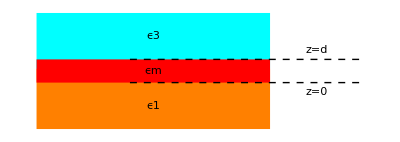

```mathematica
Graphics[{Thick,Orange,Rectangle[{-3,.3},{2,-1}],(*Thick,Green,Rectangle[{-3,-1},{2,.3}],*)Thick,Cyan,Rectangle[{-3,1.5},{2,.3}],Thick,Red,Rectangle[{-3,0},{2,.5}],Orange,Black,Dashed,Line[{{-1,0},{4,0}}],Line[{{-1,.5},{4,.5}}]},Epilog->{Text[Style["ϵm"],{-0.5,.25}],Text[Style["ϵ1"],{-.5,-.5}],Text[Style["ϵ3"],{-.5,1}],Text[Style["z=0"],{3,-.2}],Text[Style["z=d"],{3,.7}]},BaseStyle->{FontFamily->"Helvetica",FontSize->16,Black}]
```

```mathematica
(*Field Equations*)
```

```mathematica
Helmholtz1[index_]:=k0^2 ϵ[index]μ[index]-k^2+κ[index]^2 (*helmholtz equation*)

Hfield[z_,index_]:={Piecewise[{{B[index] ⅇ^(- κ[index](z))ⅇ^(ⅈ k  y (*-ⅈ ω t*))(*E0[z]*),index==1(*outside dielectric*)},{A[index] ⅇ^(κ[index](z)) ⅇ^(ⅈ k y (*-ⅈ ω t*))(*E0[z]*),index==Layers (*outside second dielectric*)}},(A[index] ⅇ^(κ[index]z)+B[index] ⅇ^(- κ[index]z))ⅇ^(ⅈ k y (*-ⅈ ω t*))(*E0[z]*)(*inside metal*)],0,0}  (*Transverse field along x*)

(*Efields corresponding to it in different directions*)Efield1[z_,index_]=ⅈ/(k0  ϵ[index])Curl[Hfield[z,index],{x,y,z}]/.{D[E0[z],z]:>0};
```

```mathematica
(*Boundary Conditions*)
```

```mathematica
d1={0,d};
(*Maxwell Boundary condition at two interfaces d=0 and d=d*)
eqns=Flatten[{(*eqnhelm*){},Flatten[Table[{Hfield[d1[[k1]],k1][[1]]==Hfield[d1[[k1]],k1+1][[1]],Efield1[d1[[k1]],k1][[2]]==Efield1[d1[[k1]],k1+1][[2]]},{k1,Layers-1}]]}]

(*values of kappas solving helmholtz*)
eqnhelm=Table[Helmholtz1[k1]==0(*Helmholtz1[k1+1]*),{k1,Layers}];
kappas=Solve[eqnhelm,{κ1,κ2,κ3}]//First;

(*variables*)
Var={A[2],κ1,B[1],A[3]};
(*solutions*)
s=Solve[eqns, Var];
```

{ⅇ^(ⅈ k y) B[1]==ⅇ^(ⅈ k y) (A[2]+B[2]),-(ⅈ ⅇ^(ⅈ k y) κ1 B[1])/(k0 ϵ1)==(ⅈ ⅇ^(ⅈ k y) (κ2 A[2]-κ2 B[2]))/(k0 ϵ2),ⅇ^(ⅈ k y) (ⅇ^(d κ2) A[2]+ⅇ^(-d κ2) B[2])==ⅇ^(ⅈ k y+d κ3) A[3],(ⅈ ⅇ^(ⅈ k y) (ⅇ^(d κ2) κ2 A[2]-ⅇ^(-d κ2) κ2 B[2]))/(k0 ϵ2)==(ⅈ ⅇ^(ⅈ k y+d κ3) κ3 A[3])/(k0 ϵ3)}

```mathematica
(*refining the solution*)
```

```mathematica
dispersion=((s[[1,2,1]]-s[[1,2,2]]==0))
```

κ1-(ϵ1 κ2 (ϵ3 κ2-ⅇ^(2 d κ2) ϵ3 κ2+ϵ2 κ3+ⅇ^(2 d κ2) ϵ2 κ3))/(ϵ2 (-ϵ3 κ2-ⅇ^(2 d κ2) ϵ3 κ2-ϵ2 κ3+ⅇ^(2 d κ2) ϵ2 κ3))==0

```mathematica
(*refining the solution*)
```

```mathematica
A11=((s[[1,2,1]]-s[[1,2,2]]))/.ⅇ^(2 d κ2)->x(*/.{ϵ2->(1-ωp^2/ω^2),k0->ω/c}*);
a1=x/.Solve[A11==0,x][[1]];
a2=((ⅇ^(2 d κ2)==a1)/.kappas);
cons[index_]:=√(k^2-k0^2 ϵ[index])->k0 ϵ[index]u[index];
kps=Table[cons[i],{i,Layers}];
a3=(a2[[1]]^-1==a2[[2]]^-1)/.kps//Simplify
Print["Thus, The dispersion relation is:  ",a3, " ,  where u=1/ϵ_i(k^2/k0^2-ϵ_i)^(1/2)"]
(*a4=(a2[[1]]==a2[[2]])/.kps//Simplify;*)
(*
(*<<EqualThread.m*)*)
(*Idd=(a3-a4)/(a3+a4)//FullSimplify*)
```

ⅇ^(2 d k0 ϵ2 u[2])==-((u[1]-u[2]) (u[2]-u[3]))/((u[1]+u[2]) (u[2]+u[3]))

Thus, The dispersion relation is:  ⅇ^(2 d k0 ϵ2 u[2])==-((u[1]-u[2]) (u[2]-u[3]))/((u[1]+u[2]) (u[2]+u[3])) ,  where u=1/ϵ_i(k/k0^2-ϵ_i)^(1/2)

```mathematica
(*Solution in Tanh Form*)
so=Solve[ⅇ^(2 x)==a2[[2]]^-1/.kps,x]/.C[1]->0;
tanhform=Tanh[ d k0 u2 ϵ2]==(Tanh[x/.so][[1]]//FullSimplify);
Print["The dispersion relation in Tanh form:   ",tanhform]
```

The dispersion relation in Tanh form:   Tanh[d k0 u2 ϵ2]==-(u[2] (u[1]+u[3]))/(u[2]^2+u[1] u[3])

```mathematica
(*For u1=u3*)
```

```mathematica
aa=tanhform/.u[3]->u[1];
Print["The dispersion relation when two dielectrics are equal:   ",aa]
```

The dispersion relation when two dielectrics are equal:   Tanh[d k0 u2 ϵ2]==-(2 u[1] u[2])/(u[1]^2+u[2]^2)

```mathematica
(*For symmetric and antisymmetric modes*)
```

```mathematica
Symmetricm=Tanh[(d k0 u[2] ϵ2)/2]==(-u[1])/u[2]
```

Tanh[1/2 d k0 ϵ2 u[2]]==-u[1]/u[2]

```mathematica
AntiSymmetricm=Tanh[(d k0 u[2] ϵ2)/2]==(-u[2])/u[1]
```

Tanh[1/2 d k0 ϵ2 u[2]]==-u[2]/u[1]

```mathematica
(*For k > > k0*)
```

```mathematica
u[index_]:=k/(k0 ϵ[index])
```

```mathematica
AntiSymmetricm//ComplexExpand//FullSimplify
```

ϵ1/ϵ2+Tanh[(d k)/2]==0

```mathematica
(*Solving this dispersion relation for antisymmetric mode*)
```

```mathematica
so=k/.Solve[AntiSymmetricm,k]/.C[1]->0/. ArcCoth[z_]:>1/2 Log[(z+1)/(z-1)]//FullSimplify;
```

```mathematica
Print["Thus, the dispersion relation for the assymetric case can be written as:     ", k==so]
```

Thus, the dispersion relation for the assymetric case can be written as:     k=={-Log[(ϵ1+ϵ2)/(ϵ1-ϵ2)]/d}